Analyze Aggregated Sales Data

Find the market sector with the highest revenue in each region

Start with a table of sales information for a company. It tracks sales by date, geographic region, market sector, product type etc.:

```mathematica
sales=Select[ResourceData["Sample Tabular Data: Sales Data"],#Date≥DateObject[{2015,7,1},"Day"]&]
```

-Graphics-

Simplify the table to show sales data by date, using Total to aggregate the values:

```mathematica
salesByDate=AggregateRows[sales,{"Quantity"->Function[Total[#Quantity]],},"Date"]
```

-Graphics-

Show the revenue and cost over time:

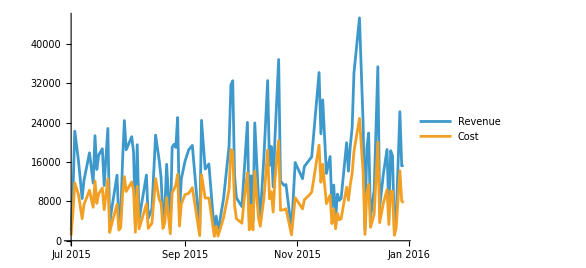

```mathematica
ListLinePlot[salesByDate->{{"Date","Revenue"},{"Date","Cost"}},]
```

Create a scatter plot of revenue vs. cost to see that the company has a very tight pricing scheme for their products:

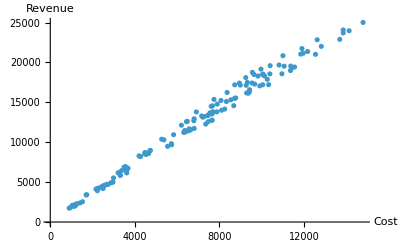

```mathematica
ListPlot[sales->{"Cost","Revenue"},]
```

Plot a histogram of the quantity column. The sales are fairly evenly distributed in size:

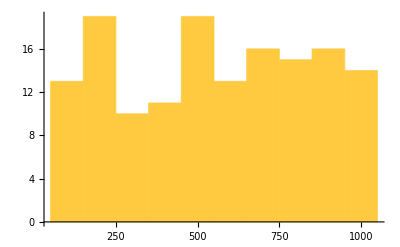

```mathematica
Histogram[sales->"Quantity"]
```

Pivot the data by region to effectively create multiple datasets:

```mathematica
salesByRegion=PivotToColumns[sales,"Region"->"Quantity"]
```

-Graphics-

Show a histogram of the number of sales of given sizes in each region:

```mathematica
Histogram[salesByRegion->{"Midwest","Northeast","South","West"},]
```

-Graphics-

Show all the regions together in a stacked histogram:

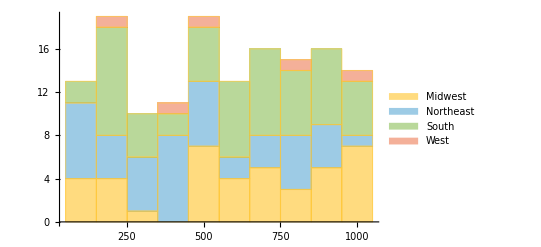

```mathematica
Histogram[salesByRegion->{"Midwest","Northeast","South","West"},]
```

Aggregate the data by region and product:

```mathematica
salesByRegion2=SortBy[AggregateRows[sales,{"Quantity"->Function[Total[#Quantity]],},{"Region","Product"}],"Region"]
```

-Graphics-

Format labels in a readable form:

```mathematica
labels=Row[#,":"]&/@;
```

Create a bar chart showing revenue by region and product:

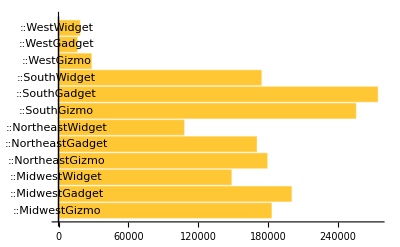

```mathematica
BarChart[salesByRegion2->"Revenue",]
```

Get the total revenue for each region and market sector:

```mathematica
salesBySector=AggregateRows[sales,{"TotalRevenue"->Function[Total[#Revenue]] },{"Region","Sector"}]
```

-Graphics-

Get a list of all the regions in the sales data:

```mathematica
regions=DeleteDuplicates[salesBySector[[All,"Region"]]]//Normal
```

{Northeast,South,Midwest,West}

Select the data for each region:

```mathematica
selectedDataByRegion=Map[
  regionName ↦ Select[salesBySector,#Region==regionName &],regions]
```

{,,,}

Find the sector with the highest revenue in each region:

```mathematica
Join@@Map[
  regionData ↦ Select[
    regionData,
    Function[record,record["TotalRevenue"]==Max[regionData[All,"TotalRevenue"]]]
  ],selectedDataByRegion]
```

-Graphics-